## Rotational wave function

```mathematica
ClearAll["Global`*"]
```

The study for a rotational wave function (its shape and evolution with the azimuthal angle ϕ).
-Graphics-

-> Define the expression of the wave function
-> Create a list of projections M for a given spin
The angle defined in Eq. (4-5) is in fact the azimuthal angle which describes the rotation around the z-axis, according to the picture shown below:
-Graphics-

```mathematica
phiM[phi_,M_]:=1/Sqrt[2π] Exp[ⅈ*M*phi];
projections[I_]:=Table[i,{i,-I,I,1}];
rephi[phi_,M_]:=If[Im[phiM[phi,M]]==0,phiM[phi,M],Re[phiM[phi,M]]];
phisquared[phi_,M_]:=Abs[phiM[phi,M]^2];
```

### Constants

```mathematica
Ifixed=3;
Mfixed=2;
```

### Study the change of φ w.r.t. to the change of azimuthal angle φ and fixed projection M

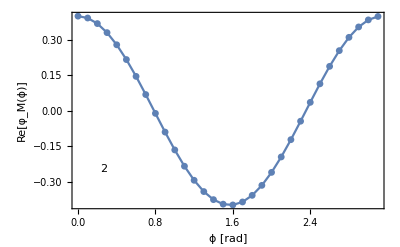

```mathematica
generateDataFixedM[M_]:=Table[{angle,rephi[angle,M]},{angle,0,π,0.1}];
plotPhiFixedM[M_]:=ListPlot[generateDataFixedM[M],Joined->True,PlotMarkers->{Automatic, Small},Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],FrameLabel->{"ϕ [rad]","Re[φ_M(ϕ)]"},Epilog->Inset[M,Scaled[{0.1,0.2}]],PlotRange->Full];
plotPhiFixedM[2]
```

```mathematica
generateDataFixedM[1]
```

{{0.,0.398942+0. ⅈ},{0.1,0.396949},{0.2,0.39099},{0.3,0.381124},{0.4,0.36745},{0.5,0.350105},{0.6,0.329261},{0.7,0.305128},{0.8,0.277946},{0.9,0.247986},{1.,0.215549},{1.1,0.180959},{1.2,0.14456},{1.3,0.106717},{1.4,0.0678071},{1.5,0.0282201},{1.6,-0.0116489},{1.7,-0.0514015},{1.8,-0.0906405},{1.9,-0.128974},{2.,-0.166019},{2.1,-0.201404},{2.2,-0.234778},{2.3,-0.265806},{2.4,-0.294178},{2.5,-0.31961},{2.6,-0.341849},{2.7,-0.360673},{2.8,-0.375892},{2.9,-0.387356},{3.,-0.39495},{3.1,-0.398597}}